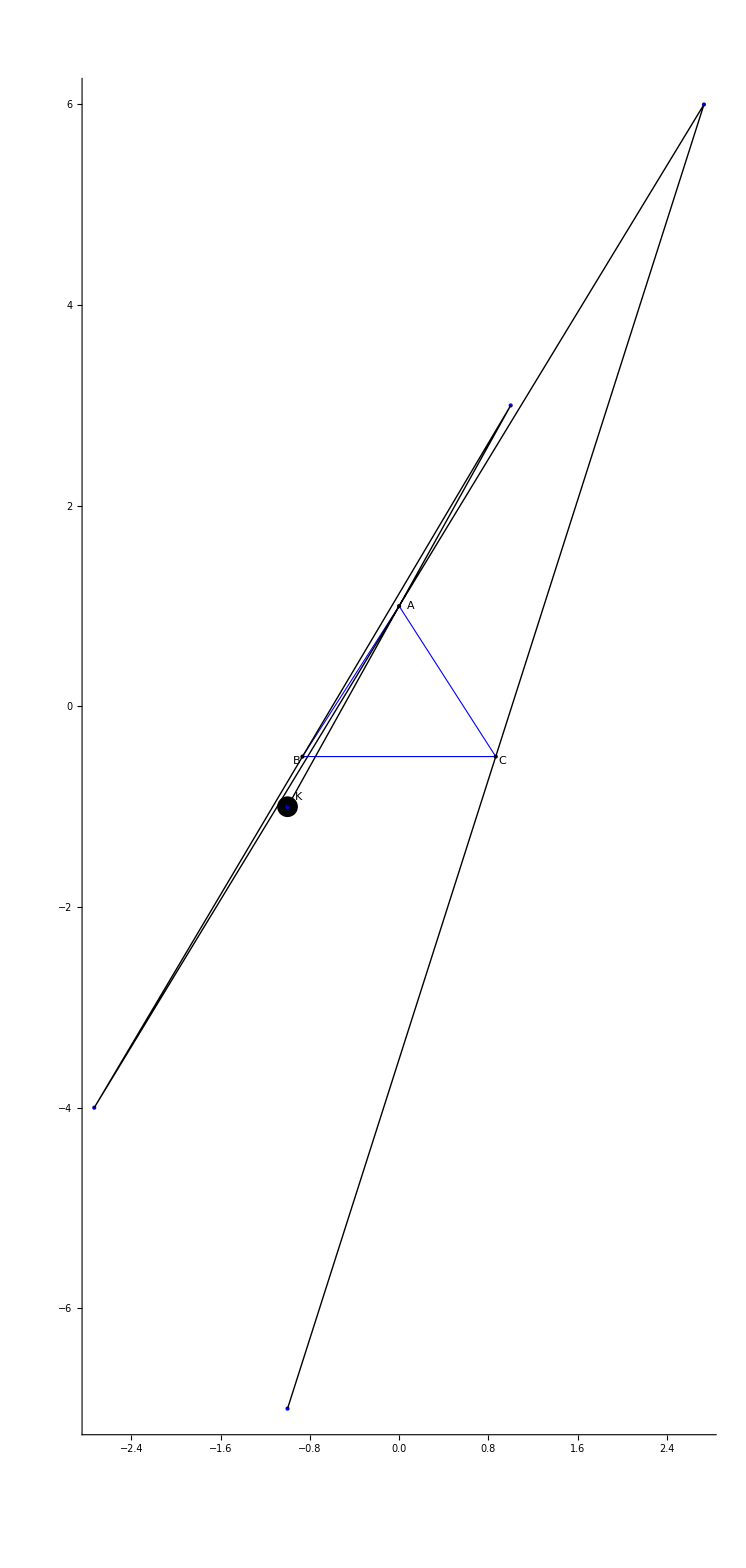

```mathematica
(*Outer Billiard problem*)
ClearAll["Global`*"];
(*Author: Evan Huynh, Marcel*)
(*Creating a triangle*)
(*Written on Mathematical 11 FrontEnd, for presentation purpose only*)
(*This might not work on Mathematica 10 or older*)
(*Cleaned version*)

(*------------Drafted function-----------------*)
(*
Create a point of reflection over a middle point
Usage: reflectPoint[{outPoint},{middlePoint}]
*)
reflectPoint[outPoint_?ListQ,middlePoint_?ListQ]:=(
xMove = -(outPoint[[1]]-middlePoint[[1]]);
yMove=-(outPoint[[2]]-middlePoint[[2]]);
{middlePoint[[1]]+xMove,middlePoint[[2]]+yMove}
)

(*graphCheck[xCoor_,yCoor_,funct_]:=(
xCoor=
)*)

(*------------Drafted function-----------------*)
fAB[x_]:=(1+Sqrt[3]*x)
fBC[x_]:=(-0.5) 
fAC[x_]:=(1-Sqrt[3]*x)
fIAB[x_]:=((x-1)/Sqrt[3]) 
fIBC[x_]:=(x)
 fIAC[x_]:=((x+1)/Sqrt[3])

(**)
(*https://mathematica.stackexchange.com/questions/66152/how-to-check-if-a-line-segment-intersects-with-a-polygon*)
checkIntersection[pointList_?ListQ]:=(
plist={InfiniteLine[pointList[[-1]],pointList[[-2]]],Polygon[CirclePoints[3]]};
Graphics`Mesh`IntersectQ[plist]
)
(**)
(*Manipulate[*)
(*-----------------*)
(*Create the first equilateral triangle*)
triangle1=Polygon[CirclePoints[3]];
xA=0;yA=1; pointA={xA,yA}; textA= Text["A",{0.1,1}];
xB=-(√3)/2;yB=-1/2; pointB={xB,yB}; textB = Text ["B",{-0.92,-0.54}];
xC=(√3)/2; yC=-1/2; pointC={xC,yC}; textC = Text["C",{0.92,-0.54}];
xK=-1;yK=-1; pointK={xK,yK}; textK=Text["K",{xK+0.1,yK+0.1}];
pointList={pointK};

(*Add everything to the plot2 initially*)
plot2={EdgeForm[Directive[Thick,Blue]],Directive[White],triangle1,Directive[Black],Point[pointA],Point[pointB],Point[pointC],textA,textB,textC,PointSize[0.02],Point[pointK],textK};
(*Check location of the point*)
point1=pointA;point2=pointB;point3=pointC;

(*Define point 1, 2, 3.*)
(*Add point to list*)
doCtimes=5; doCtimes=Floor[doCtimes];

rI=3;
pointList={pointK};
(*pointList=AppendTo[pointList,reflectPoint[Last[pointList],point1]];*)
Do[rI=RandomInteger[{1,3}];
If[rI==1,
If[checkIntersection[pointList],pointList=Drop[pointList,-1],pointList=AppendTo[pointList,reflectPoint[Last[pointList],point1]];];
,If[rI==2,
If[checkIntersection[pointList],pointList=Drop[pointList,-1],pointList=AppendTo[pointList,reflectPoint[Last[pointList],point2]];];
,If[rI==3,
If[checkIntersection[pointList],pointList=Drop[pointList,-1],pointList=AppendTo[pointList,reflectPoint[Last[pointList],point3]];];
]
]
]
,doCtimes]


plot3={Blue,Point[pointList],Black,Line[pointList]};
plot4={plot2,plot3};

(*Export the result*)
plot4={plot2,plot3};
Show[Graphics[plot4],Axes-> True,AxesStyle->Black]
(*-----------------*)
(*,{{xK,2,"x-coordinate"},-5,5},{{yK,2,"y-coordinate"},-5,5},{{doCtimes,5,"Number of movements"},0,10}]*)
(*--------------END----------------*)
```